# Functional Programming in Mathematica

Anton Antonov

book for Wiley 2009-2010

## Introduction

The goal of this chapter is to give the reader a quick and useful introduction to the programming language of Mathematica.

Most books about programming in Mathematica take a sort of linguistic approach in which the operators and commands are explained through expression re-writing and transformations. In my opinion this approach is found to be very useful by people who consider writing programming code and mathematical formulas their primary call in life. For people who are more interested in knowing about nature or putting together physical devices that transform actual matter, in my opinion, it is better to take the approach of showing programming constructs as a flow between the states in the computational model used by Mathematica (or any other system).

In this chapter we are going to invent and built a core subset of the Mathematica's programming language and use flow charts to explain the programming primitives that are most frequently useful. Flow charts have very few elements (we are going to use four elements in this book) and we can claim that any program in any language can be expressed with them.

In this book the flow charts are mainly used as visual representation of the implementation of the programming primitives. Hopefully this would make the learning of the programming primitives easy and solid. (I.e. easy to understand and remember, easy to see how to use while programming more complicated algorithms.)

### Inventing Mathematica's language

Everything is a function even the data:

```mathematica
9//Head
```

Integer

Most functions are polymorphic -- they act on parametrized types. (This is different from the polymorphism in OO.)

For different arguments we can have different code corresponding to the function signature. In this way the program can have an execution path that depends on the input data (or parameters).

Instead of considering how the memory changes because of the input data and the algorithms we develop, we can consider what transformations are done to the data. Obviously we can have compositions of functions. We can also have conditional functions, that produce a result using different formulas (code) for different conditions satisfied by the arguments.

### Programming languages

We can look at computer programming as a way to fully specify mathematical and algorithmic models of natural, technological, and social interaction processes. Computer programming languages are made with certain model of computation in mind, which, roughly speaking, postulates the elements and operations of the computing machine, and how the programming code is executed on it.

Computer programming languages bear similarities with the natural languages and the language of mathematics. Let us shortly examine the use of natural languages for describing space-time events. First, we will say that the physical reality (space-time) has objects and phenomena. The order between the objects gives us the idea of space, and the order between the phenomena gives us the idea of time. In a spoken language we name the objects, and we use processes to describe the order of the phenomena. We can have language expressions that formulate how an object or a group of objects interact with other objects. For example, the expression "five humans walk on the road" describes five objects doing a process on a sixth object.

### What features the best language would have

### Patterns

Mathematical formulas, as

(x+y)^2=x^2+2 x y +y^2,

can be seen as rules to replace any mathematical expression that has the same form (or pattern) as the left hand side with the right hand side. The symbols and expressions found in correspondence with the free variables in the left hand side are substituted in the right hand side. The names of the variables are needed to make

It is important to recognize

with the corresponding values used to make the match with the left hand side used in right hand side.

Every assignment in Mathematica can be seen as a rule of rewriting. We have two types of assignments: immediate and delayed.

### Mathematica's programming language features

What makes Mathematica's programming language very expressive and efficient is the combination of several closely knit features.

1. Rich (and consistent) set of second order functions. Mathematica have programming primitives for the most frequent types of recursion, that makes writing code more convenient.

2. Pattern matching of arguments and data. Mathematica can tell does the value of a variable or a function argument have a certain structure  or adheres to a certain template or stencil. This is used to specify and implement polymorphic behaviour of the programs we write.

3. Data and programs have the same structures and operations over them. In other words, programs can be treated as data if and when that is needed. In most cases we transform data collections into a sequence of function arguments.

4. Having both dynamic and lexical scoping of variables. The way lexical scoping is implemented in Mathematica allows for the use of the powerful concept of closures. Dynamic scoping and closures can be used to provide execution polymorphism.

### Constructing algorithms

When modeling chemical or physical phenomena we need to restrict ourselves to a certain level of detail and adopt certain simplifying assumptions. The assumptions and physical laws become the invariants our algorithms would  leverage upon or have to maintain or approximate.

In general programming languages can be classified into three groups:

1. Imperative languages that make description of how objects interact with each other,

2. Functional languages a better at describing processes.

3. Declarative .

Writing programming code is about automation of symbolic or numerical transformations of a certain type of data. We need to realize what invariants hold about

### Philosophical background (first)

We can look at computer programming as a way to model the world. Computer programming languages bear similarities with the natural languages and the language of mathematics. Let us shortly examine the use of natural languages for describing space-time events. First, we will say that the physical reality (space-time) has objects and phenomena. The order between the objects gives us the idea of space, and the order between the phenomena gives us the idea of time. In a spoken language we name the objects, and we use processes to describe the order of the phenomena. We can have language expressions that formulate how an object or a group of objects interact with other objects. For example, the expression "five humans walk on the road" describes five objects doing a process on a sixth object. We can designate the speech that uses such language expressions as object-centric speech. We can have speech with language expressions that are process-centric and the participants in the process are implied or stated in a sub-ordinated manner. For example, we can say "five human road walkings," and instead of thinking and speaking of objects as humans or roads that perform actions on each other, we can think and speak with the idea that the process of walking requires a walker and a walkee. Further, we can think of the process of being a human and the process of being a road i.e. "humanness" and "roadness."

We can say that imperative programming languages (C++, FORTRAN, Pascal) have take the object-centric or state-centric point of view, and functional programming languages (LISP, Mathematica, ML) take the process-centric point of view.

### Philosophical background

We can look at computer programming as a way to model the world. Computer programming languages bear similarities with the natural languages and the language of mathematics. Let us shortly examine the use of natural languages for describing space-time events. First, we will say that the physical reality (space-time) has objects and phenomena. The order between the objects gives us the idea of space, and the order between the phenomena gives us the idea of time. In a spoken language we name the objects, and we use processes to describe the order of the phenomena. We can have language expressions that formulate how an object or a group of objects interact with other objects. For example, the expression "five humans walk on the road" describes five objects doing a process on a sixth object.

Spelling out all the interactions and transformations one by one can be long and inconvenient. That is why ...

We can have programming languages that describe changing states, or programming languages that describe processes. ???

In mathematics there is a tendency to introduce algebraic operations into the subject of study. After algebraic transformation rules are derived and used to derive or prove connections that would be hard to reach just by reasoning with core, non-algebraic laws of the subject of study. For example, Analytical Geometry reduces to geometrical problems to systems of algebraic equations, and Functional Analysis reduces systems of partial differential equations to systems of algebraic ( in many cases linear) equations.

A general approach in mathematics [[...]]

### Data structures and algorithms

### Flow chart elements

In this book we are going to use  four flow chart elements. Their names are Input/Output block, Processing block, Decision block, and Arrow. Below is given an example of a flow chart that represents the calculation of the total money amount for purchasing a collection of selected grocery items. The Input/Output block is represented with parallelogram. Inside the Input/Output block are written input or starting data and arguments, or output results. The Processing block is represented with a rectangular. In the Processing blocks are written assignments or sequence of assignments. The Decision block is represented with a rhombus and contains True/False tests. The Arrow element is represented with lines with arrow heads. An instance of the Arrow element starting at a block and ending at another block represents that the next algorithm step to be executed is the block the arrow points to.

The algorithm to find the total sum (total money value) of the items in the grocery card is simple. We start with the total sum being zero. Until the grocery cart is empty, we pick an item from the cart, we find its price, and we add that price to the total sum. At the point where there are no more items in the cart, the total sum is the result we are looking for.

The flow chart describes the steps of this algorithm. The first block, the Input/Output block 1, says that the input for the algorithm is a grocery cart. From Input/Output block 1 we move to the Processing block 2, which assigns zero to a variable named "total sum." From the Processing block 2 we move to the Decision block 3, that asks is the cart empty. If the answer of the question in the Decision block 3 is "No," then we proceed to the Processing block 5, which prescribes taking and item from cart and finding its price. After the Processing block 5 we go to Processing block 6, which prescribes adding the price of the item picked in Processing block 5 to "total sum." From Processing block 6 we go to Processing block 7, that prescribes placing the item in a place different than the cart (otherwise the algorithm would not finish). From Processing block 7 we go to the Decision block 3, to check is the cart empty or not.  The positive answer, "Yes," of this question would bring the algorithm to an end with the Input/Output block 4 that outputs the value of the variable "total sum."

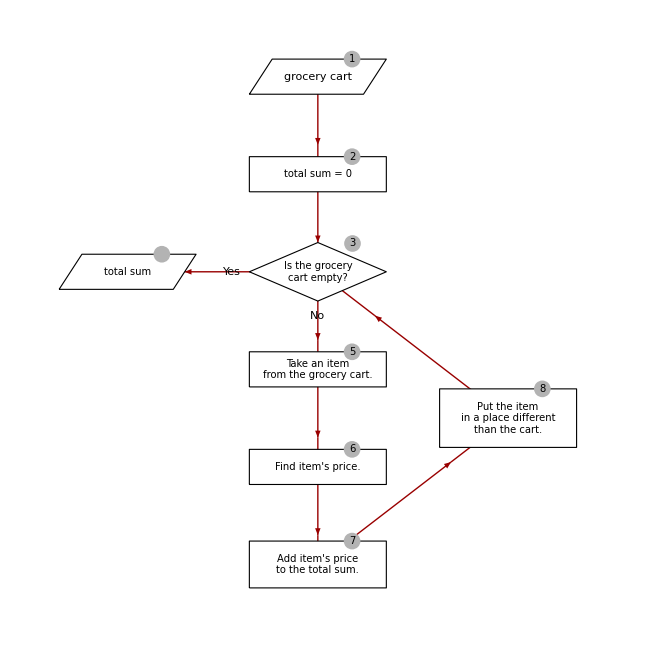

```mathematica
DefineGroceryCardVertex[{ffont_,fsize_,factor_}]:=
Block[{},
Clear[GroceryCardVertex,GroceryCardGraph];
GroceryCardVertex[coords_,"input"]:=
IOElement[coords,{1,0.3}factor,
InputDescription[{{"grocery cart",""}},ffont,fsize]
];
GroceryCardVertex[coords_,"init"]:=ProcessingElement[coords,{1.2,0.3}factor,Style["total sum = 0",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"indcond"]:=DecisionElement[coords,{1.2,0.5}factor,Style["Is the grocery\ncart empty?",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"applyfunc"]:=ProcessingElement[coords,{1.2,0.3}factor,Style["Take an item\nfrom the grocery cart.",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"applyfunc2"]:=ProcessingElement[coords,{1.2,0.3}factor,Style["Find item's price.",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"append"]:=ProcessingElement[coords,{1.2,0.4}factor,Style["Add item's price\nto the total sum.",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"indincr"]:=ProcessingElement[coords,{1.2,0.5}factor,Style["Put the item\nin a place different\nfrom the cart.",fsize,FontFamily->ffont]];
GroceryCardVertex[coords_,"res"]:=
IOElement[coords,{1,0.3}factor,Style["total sum",fsize,FontFamily->ffont]];
GroceryCardGraph[]:={"input"->"init","init"->"indcond",{"indcond"->"res","Yes"},{"indcond"->"applyfunc","No"},"applyfunc"->"applyfunc2","applyfunc2"->"append","append"->"indincr","indincr"->"indcond"}
];
DefineGroceryCardVertex[{"Times",12,1.2}]
DownDefineNumeratedVertex[DefineGroceryCardVertex,{"Times",12,1.2},{10,RGBColor[0.7,0.7,0.7]}]
DefineGroceryCardVertexNumerated[{"Times",10,1.2}]
LayeredGraphPlot[GroceryCardGraph[],VertexCoordinateRules->-{{0,0},{0,1},{0,2},{2,2},{0,3},{0,4},{0,5},{-2,3.5}},VertexRenderingFunction->(GroceryCardVertex[#1,#2]&),EdgeRenderingFunction->({RGBColor[0.6,0,0],Arrowheads[0.02], MidArrow[#1,#2,#3,"Ratio"->0.7,"LabelRatio"->0.45]}&),ImageSize->650]
```

In Mathematica the algorithm above can be easily specified as "take the prices of all items in cart and sum them."

### Flow chart elements and

Instead of

### Other

One of the goals of this chapter is to be used as a reference to quickly grasp what a function does.

Our knowledge of the total money amount we have to pay for the groceries in the card is going to change while we scan the items. We are going to use are the name "total sum" for the money value of the items taken out of the shopping cart.

### Section code

## Evaluation loop

## Basic Definitions

### Expressions

The concept of expression is fundamental in Mathematica. Everything in Mathematica is an expression: the correct input for adding two values, like 2+π, is an expression, a graphic is an expression, a Mathematica's notebook is an expression.

Each expression has the form  head[] or head[arg_1, arg_2, ..., arg_n] . The head of an expression can be found using the function Head:

```mathematica
Head[Integrate[f[x], {x, 0, a}]]
```

Integrate

Mathematica represents all expressions using arithmetic operations in familiar mathematical form. For example, expressions of the form Plus[arg_1, arg_2,..., arg_n]would be printed out, and can be input as arg_1+arg_2+...+arg_n. This can be demonstrated using the function FullForm:

```mathematica
FullForm[2+π]
```

Plus[2,Pi]

Another shorthand is using {expr_1,expr_2,..., expr_n} for the expressions List[expr_1,expr_2,..., expr_n].

Examples are given below. More examples and discussion about expressions can be found in the tutorial "" and the guide page "."

#### An arithmetic expression

Consider the mathematical expression 1+4(1+x)^2 . In Mathematica this expression is represented as:

```mathematica
Plus[1,Times[4,Power[Plus[1,x],2]]]
```

1+4 (1+x)^2

The output is the shorthand version of the expression. Mathematical expressions can be entered with their shorthand versions, and using FullForm we can see their internal representations:

```mathematica
1+4 (1+x)^2
```

1+4 (1+x)^2

```mathematica
FullForm[1+4 (1+x)^2]
```

Plus[1,Times[4,Power[Plus[1,x],2]]]

#### List expression

This is a list of numbers and symbols

```mathematica
{1,2,a,b}
```

Its full expression form is

```mathematica
FullForm[{1,2,a,b}]
```

List[1,2,a,b]

and its head is List:

```mathematica
Head[{1,2,a,b}]
```

List

#### Graphics

Here are the full expression form and head of a graphic.

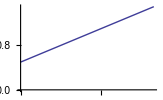
```mathematica
FullForm[-Graphics-]
```

Graphics[List[List[],List[],List[Hue[0.67,0.6,0.6],Line[List[List[1.×10^-6,0.500001],List[0.999999,1.5]]]]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,True],Rule[AxesOrigin,List[0,0]],Rule[ImageSize,List[164.,Automatic]],Rule[PlotRange,List[List[0,1],List[0,1.5]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[Scaled[0.02],Scaled[0.02]]]]

```mathematica
Head[-Graphics-]
```

Graphics

#### Interactive elements

Interactive elements are also expressions.

```mathematica
"Click me"//FullForm
```

Button["Click me",Print["You did it!"],Rule[Appearance,Automatic],Rule[Evaluator,Automatic],Rule[Method,"Preemptive"]]

```mathematica
"Click me"//Head
```

Button

#### Mathematical expressions table

In the table below are listed mathematical expressions and their full forms and heads.

```mathematica
exprs={HoldForm[2+2],HoldForm[2*2],HoldForm[2/5],HoldForm[2^10],y^k,1+4*(x+12),HoldForm[Log[2,20]],HoldForm[D[Power[x,2],x]],Integrate[f[x],{x,0,a}]};
forms={"Plus[2,2]","Times[2,2]","Divide[2,5]","Power[2,10]",FullForm[y^k],FullForm[1+4*(x+12)],"Log[2,20]","D[Power[x,2],x]","Integrate[f[x],{x,0,a}]"};
heads={Plus,Times,Divide,Power,Power,Plus,Log,D,Integrate};
Grid[Prepend[Transpose[{exprs,forms,heads}],{Style["Expressions ",Italic,Bold],Column[{Style["Results of applying",Italic,Bold],Style["FullForm",Bold]}],Column[{Style["Results of applying",Italic,Bold],Style["Head",Bold]}]}],Alignment->Left,Dividers->{{False,False,False},{True,True,False}}]
```

Expressions  | Results of applying
FullForm | Results of applying
Head
2+2 | Plus[2,2] | Plus
2 2 | Times[2,2] | Times
2/5 | Divide[2,5] | Divide
2^10 | Power[2,10] | Power
y^k | Power[y,k] | Power
1+4 (12+x) | Plus[1,Times[4,Plus[12,x]]] | Plus
Log[2,20] | Log[2,20] | Log
∂_x x^2 | D[Power[x,2],x] | D
∫_0^a f[x]ⅆx | Integrate[f[x],{x,0,a}] | Integrate

### Atoms

Atoms are expressions that cannot be subdivided into subexpressions. Symbols, numbers, and strings are atoms. (Later on we will see that the objects called "" are also atoms.)

The function AtomQ can be used as a test to find out if an expression is an atom or not. Complex numbers although represented as sums of real and imaginary parts are also atoms. Consider these examples:

```mathematica
AtomQ[Complex[3,4]]
```

True

```mathematica
Complex[3, 4]⟦1⟧
```

(3+4 ⅈ)⟦1⟧

The following table shows various expressions with the atomic test applied to them and the heads of the expressions.

```mathematica
objects={5,3/4,3.1415926,2+ⅈ 3,π,x,"\"fine day\"",SparseArray[{10->1,12->1},{20}],2+π,Integrate[f[x],{x,0,1}],{1,{2,a},3}};
Grid[Prepend[Map[Through[{Identity,AtomQ,Head}[#]]&,objects],Style[#,Bold]&/@{"Expression","AtomQ","Head"}],Alignment->Left,Dividers->{{False},{True,True,False}}]
```

Expression | AtomQ | Head
5 | True | Integer
3/4 | True | Rational
3.14159 | True | Real
2+3 ⅈ | True | Complex
π | True | Symbol
x | True | Symbol
"fine day" | True | String
SparseArray[<2>,{20}] | True | SparseArray
2+π | False | Plus
∫_0^1 f[x]ⅆx | False | Integrate
{1,{2,a},3} | False | List

In functional languages everything is an expression composed of functions, so, for consistency, atoms should be able to be seen as functions. For example, an atom that is an integer number can be seen as the function Integer applied to some numeric representation of the number and returning that number as a result.

More about atoms can be found in the tutorial "" and the guide page "."

### Patterns

Using patterns we can specify sets of expressions, expressions that adhere to a certain form. Pattern matching is the process of testing does a given expression belong to the set of expressions specified by the pattern with which the test is performed.

For example, the pattern

```mathematica
{_, _}
```

which translates to "a list of two expressions" would match any of the expressions in this table

```mathematica
Column[{{2,π},List["someString",5],{f[x,y],t^4}}]
```

{2,π}
{someString,5}
{f[x,y],t^4}

The full expression form of {_,_} is

```mathematica
FullForm[{_,_}]
```

List[Blank[],Blank[]]

The pattern Blank[] matches any expression and other than actual atoms it is the simplest pattern. As a shorthand of Blank[] the underscore symbol, _, is used. Using MatchQ we can find does an expression match a pattern:

```mathematica
MatchQ[{2,π},{_,_}]
```

True

If we take any expression and we replace with Blank[] any atom, or sub-expression, or the expression itself, we are going to produce a valid pattern.  The expression itself can be used as a pattern too. For example, from f[x,y] we can derive these patterns:

```mathematica
Riffle[{f[x,y],f[_,y],f[x,_],f[_,_],_[x,y],_[_,y],_[x,_],_[_,_],_},"   "]//Row
```

f[x,y]   f[_,y]   f[x,_]   f[_,_]   _[x,y]   _[_,y]   _[x,_]   _[_,_]   _

For example the pattern _[_, _] would match any expression that has the form head[arg_1,arg_2] as the following:

```mathematica
TableForm[{2+π,{a,b},f[a,b],"stringHead"["stringArg",5],Integrate[f[x],{x,0,1}],M[{a1,a2},{b1,b2,b3}]},TableDepth->1]
```

2+π
{a,b}
f[a,b]
stringHead[stringArg,5]
∫_0^1 f[x]ⅆx
M[{a1,a2},{b1,b2,b3}]

Being able to produce (and match) patterns with the procedure described above is already a good pattern matching functionality. We can extend it and generalize it in two obvious directions. One is to allow matching of sequences of expressions. (It would be hard to specify just using Blank[] an expression that has arbitrary or very large number of sub-expressions.) The other generalization direction is to allow imposing restrictions of the objects matched by (i) a single Blank[], and (ii) by the whole pattern.

Sequences of expressions are matched with the patterns BlankSequence[] and BlankNullSequence[]. The pattern BlankSequence[] matches any sequence of expressions and has the shorthand __. The pattern BlankNullSequence[] matches any sequence of expressions or no expression and has the shorthand ___ . The table below shows the application of MatchQ with different list expressions and different patterns.

```mathematica
fs={f[],f[1],f[1,2],f[1,2,3],{},{1},{1,2},{1,2,3}};
ps={f[Blank[]],f[BlankSequence[]],f[BlankNullSequence[]],_[_],_[__],_[___]};
tbl=Outer[MatchQ,fs,ps,1];
Grid[MapThread[Prepend,{Join[{{"",Style["patterns",Bold,Italic],SpanFromLeft},ps},tbl],Join[{"",Style["expressions",Bold,Italic]},fs]},1],Alignment->Left,Dividers->{{False,True,False},{False,True ,True,False}}]
```

|  | patterns |  |  |  | 
expressions | f[_] | f[__] | f[___] | _[_] | _[__] | _[___]
f[] | False | False | True | False | False | True
f[1] | True | True | True | True | True | True
f[1,2] | False | True | True | False | True | True
f[1,2,3] | False | True | True | False | True | True
{} | False | False | False | False | False | True
{1} | False | False | False | True | True | True
{1,2} | False | False | False | False | True | True
{1,2,3} | False | False | False | False | True | True

Using the form Blank[h] we can restrict the pattern matching of Blank[] only to expressions that have the head h. For example, we can find all the integers in a sequence of numbers using atom head matching and the function Cases that gives the values in a expressions that match a pattern:

```mathematica
Cases[{2.494,1,5.54,5,6.1,3,6.626,3.5,10,7},_Integer]
```

{1,5,3,10,7}

Further we can match a sequence of expressions with same head using the pattern specification Repeated[Blank[h]] and RepeatedNull[Blank[h]] that have the shorthand _h.. and _h... respectively. For example, we can check that a list of expressions is a non-empty list of strings:

```mathematica
MatchQ[{"Li","Na","Rb","Cs","Fr"},{_String..}]
```

True

Here is table of the results of MatchQ applied to different expressions using different patterns.

```mathematica
fs={f[],f[1],f[1,2],f[1,2,3],{},{1},{1,2},{1,2,3}};
ps={_f,f[_Integer..],f[_Integer...],_List,{_Integer..},{_Integer...}};
tbl=Outer[MatchQ,fs,ps,1];
Grid[MapThread[Prepend,{Join[{{"",Style["patterns",Bold,Italic],SpanFromLeft},ps},tbl],Join[{"",Style["expressions",Bold,Italic]},fs]},1],Alignment->Left,Dividers->{{False,True,False},{False,True ,True,False}}]
```

|  | patterns |  |  |  | 
expressions | _f | f[_Integer..] | f[_Integer...] | _List | {_Integer..} | {_Integer...}
f[] | True | False | True | False | False | False
f[1] | True | True | True | False | False | False
f[1,2] | True | True | True | False | False | False
f[1,2,3] | True | True | True | False | False | False
{} | False | False | False | True | False | True
{1} | False | False | False | True | True | True
{1,2} | False | False | False | True | True | True
{1,2,3} | False | False | False | True | True | True

Patterns can be named. A named pattern has the form Pattern[name,pattern]. A shorthand for Pattern[name,_] is name_ . Sometimes pattern naming is necessary because of Mathematica's eager evaluation strategy. For example, this would not give a match:

```mathematica
MatchQ[3+π,_+_]
```

False

But this would

```mathematica
MatchQ[3+π,x_+y_]
```

True

The reason is that because of the eager evolution _+_ ( with full form Plus[_,_]) is evaluated to 2 _ ( with full form Times[2,_]) and the later is used for pattern matching.

Sometimes we need to specify and additional condition to the patterns using Condition[pattern,cond] :

```mathematica
Cases[{2.494,1,5.54,5,6.1,3,6.626,3.5,10,7},n_Integer/;OddQ[n]]
```

{1,5,3,7}

which is equivalent to :

```mathematica
Cases[{2.494,1,5.54,5,6.1,3,6.626,3.5,10,7},Condition[Pattern[n,Blank[Integer]],OddQ[n]]]
```

{1,5,3,7}

Pattern finding in data, nature processes, or object and subject behaviours is a fundamental human activity. Therefore i

Pattern matching can be used f	or explore both data and code, since everything in Mathematica is an expression.

The parts of a pattern can be named and given additional conditions.

More about patterns can be found in the tutorial "" and the guide page "."

#### Examples

Check matching with the pattern {_,_}:

```mathematica
MatchQ[{f[x, y] , t^4},{_,_}]
```

True

```mathematica
MatchQ[{f[x, y] , t^4,g[x,y]},{_,_}]
```

False

Find all the integers in a number sequence using atom head matching:

```mathematica
Cases[{2.494,1,5.54,5,6.1,3,6.626,3.5,10,7},_Integer]
```

{1,5,3,10,7}

Find all odd integers in a sequence using atom head matching and a pattern condition:

```mathematica
Cases[{2.494,1,5.54,5,6.1,3,6.626,3.5,10,7},n_Integer/;OddQ[n]]
```

{1,5,3,7}

Consider the following list that consists of sub-lists each of which corresponds to a chemical compound. The sub-lists have the form {compound formula, {elem_1,n_1}, {elem_2,n_2},...,{elem_k,n_k}}:

```mathematica
{{"H2O",{"H",2},{"O",1}},{"CO2",{"C",1},{"O",2}},{"SO2",{"O",2},{"S",1}},{"NH3",{"H",3},{"N",1}},{"NaCl",{"Na",1},{"Cl",1}}}
```

Using pattern matching with the command Cases we can retrieve all sub-lists representing compounds that have two atoms of oxygen. The matching pattern is {___, {"O", 2}, ___} that translates to: any sequence of expressions, followed by a list of the atoms "O" and 2, followed by any sequence of expressions. Note that the pattern matching is made only at level 1.

```mathematica
Cases[
{{"H2O",{"H",2},{"O",1}},{"CO2",{"C",1},{"O",2}},{"SO2",{"O",2},{"S",1}},{"NH3",{"H",3},{"N",1}},{"NaCl",{"Na",1},{"Cl",1}}}
,{___,{"O",2},___},{1}]
```

{{CO2,{C,1},{O,2}},{SO2,{O,2},{S,1}}}

### Levels

We can represent each expression as a tree in the following way:

The head of the expression is the root of the tree.

Each atom is a vertex of the tree.

If a sub-expression is not an atom, i.e. it has the form head[subexpr_1,subexpr_2...], then its head is a vertex.

The sub-expressions subexpr_1,subexpr_2... of head[subexpr_1,subexpr_2...] are children of head.

The level of an atom is the distance between the root and the vertex representing the atom. The level of a sub-expression is the distance between the root and sub-expression's head.

For example, the expression {4,x,Log[y^2]} has the full form

```mathematica
FullForm[{4, x, Log[y^2]}]
```

List[4,x,Log[Power[y,2]]]

and its tree form is

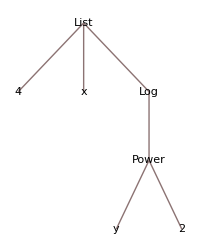

```mathematica
TreeForm[{4, x, Log[y^2]},ImageSize->200]
```

We say that the atom List is at level 0, the atoms 4, x, and Log are at level 1, the atom Power is at level 2, and the atoms y and 2 are at level 3. The sub-expression Power[y,2] is at level 2, the same level as the level of the atom Power.

### Rules

One natural, straightforward transformation of a data expression is to replace a set of sub-expressions with the elements of another corresponding set of expressions. In Mathematica this is best done with patterns, rules, and the functions Replace and ReplaceAll. As it is described in the previous sub-section, "Patterns," patterns are used to specify sets of expressions. Rules, discussed in this sub-section, are used to specify (transformational) correspondences. A correspondence or association between two expressions is specified in a rule form as Rule[e,ce] or with shorthand notation e→ce. For example, let us replace the integers in a list of numbers with their square:

```mathematica
ReplaceAll[{1.6,2,3.2,{3,4},4.1,5},n_Integer->n^2]
```

{1.6,4,3.2,{9,16},4.1,25}

The function ReplaceAll attempts to apply the transformation rules to all subexpressions of its first argument. If we want to transform the integers only at a given level we can use Replace which takes a level specification argument. For example, with the following command

```mathematica
Replace[{1.6,2,3.2,{4,3},4.1,5},n_Integer->n^2,{2}]
```

{1.6,2,3.2,{16,9},4.1,5}

we transform only the numbers in the sub-list of integers of the data argument.

Another example is the following in which we transform only the subscripts numbers of the symbols:

```mathematica
Replace[{2,3,Subscript[T, 3],Subscript[A, 4],Subscript[M, 2]},n_Integer->n^2,{2}]
```

{2,3,T_9,A_16,M_4}

Compare with

```mathematica
ReplaceAll[{2,3,Subscript[T, 3],Subscript[A, 4],Subscript[M, 2]},n_Integer->n^2]
```

{4,9,T_9,A_16,M_4}

### Delayed rules

When a rule is constructed with Rule[p,cexpr] both p and cexpr are immediately evaluated. This can be seen in the following example:

```mathematica
Rule[_ _,Cos[π/2]]
```

_^2→0

In some cases we want to postpone the evaluation until the actual application of the rule. For example, if we want to replace with zeroes all the symbols in a list of numbers and symbols we can not do it using Rule:

```mathematica
Replace[{x,2,r,t,6,m,8},n_?AtomQ->If[Head[n]===Symbol,0,n],{1}]
```

{0,0,0,0,0,0,0}

What happens is that the rule given to Replace is evaluated to n_?AtomQ→0:

```mathematica
n_?AtomQ->If[Head[n]===Symbol,0,n]
```

n_?AtomQ→0

So a different kind of rules are needed, that do not evaluate their second argument. That type of rules are called delayed evaluation rules and have the form RuleDelayed[p,dexpr]. or in shorthand p:>dexpr. Using a delayed evaluation rules we can replace with zeroes only the symbols:

```mathematica
Replace[{x,2,r,t,6,m,8},n_?AtomQ:>If[Head[n]===Symbol,0,n],{1}]
```

{0,2,0,0,6,0,8}

The second argument of RuleDelayed (or the right hand expression in the shorthand notation :>)  is not evaluated:

```mathematica
n_?AtomQ:>If[Head[n]===Symbol,0,n]
```

n_?AtomQ:>If[Head[n]===Symbol,0,n]

Its evaluation is postponed until the pattern n is matched with an expression.

The easiest way to demonstrate this is to use a replacing expression that gives different value every time it is evaluated. For example, suppose that we want to replace all integers in a list of numbers with different randomly generated integers. 
Use like RandomReal[] or Increment[n].

```mathematica
Replace[{a,b,c},x_?AtomQ->x+RandomReal[],1]
```

{0.395215+a,0.395215+b,0.395215+c}

```mathematica
Replace[{a,b,c},_?AtomQ:>RandomReal[],1]
```

{0.372084,0.475214,0.772294}

#### replacing examples study

```mathematica
Replace[{1.6,Subscript[T, 5],3.2,4,4.1},n_Integer:>n^2,3]
```

{1.6,T_25,3.2,16,4.1}

```mathematica
ReplaceRepeated[{1.6,4,3.2,4,4.1},{n_Integer:>n^2,n_?NumberQ:>Ceiling[n]}]
```

{Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]}

```mathematica
ReplaceRepeated[{1.6,4,3.2,4,5.1},{n_Integer->x,(n_?(Not[IntegerQ[#]]&)):>Ceiling[n]}]
```

{2,4,4,4,6}

```mathematica
ReplaceAll[{1.6,4,3.2,4,5.1},{n_Integer:>x,(n_?(Not[IntegerQ[#]]&)):>Ceiling[n]}]
```

{2,4,4,4,6}

```mathematica
ReplaceRepeated[{1.6,20,3.2,40,5.1},{n_Integer:>x,(n_?(Not[IntegerQ[#]]&)):>Ceiling[n]}]
```

{2,20,4,40,6}

```mathematica
Replace[{1.6,20,3.2,40,5.1},n_Integer->x,1]
```

{1.6,x,3.2,x,5.1}

```mathematica
n=.
```

#### Solve

```mathematica
ReplaceAll[{1.6,2,3.2,4,4.1},n_Integer:>First[Solve[x^n+x+1==0,x]]]
```

{1.6,{x→-(-1)^(1/3)},3.2,{x→1/2 √((1/2 (9+ⅈ √687))^(1/3)/3^(2/3)+4/(3/2 (9+ⅈ √687))^(1/3))-1/2 √(-(1/2 (9+ⅈ √687))^(1/3)/3^(2/3)-4/(3/2 (9+ⅈ √687))^(1/3)-2/(√((1/2 (9+ⅈ √687))^(1/3)/3^(2/3)+4/(3/2 (9+ⅈ √687))^(1/3))))},4.1}

```mathematica
ReplaceAll[{1.6,2,3.2,4,4.1},n_Integer->First[Solve[x^n+x+1==0,x]]]
```

{1.6,1+x+x^2==0,3.2,1+x+x^4==0,4.1}

#### Head of an Atom

```mathematica
Replace[{x,2,r,t,6,m,8},n_?AtomQ->If[Head[n]===Symbol,0,n],{1}]
```

{0,0,0,0,0,0,0}

```mathematica
Replace[{x,2,r,t,6,m,8},n_->If[Head[n]===Symbol,0,n],∞]
```

{0,0,0,0,0,0,0}

```mathematica
Replace[{x,2,r,t,6,m,8},n_:>If[Head[n]===Symbol,0,n],∞]
```

{0,2,0,0,6,0,8}

```mathematica
Replace[{x,2,{r,t,4},{6,m},8},n_->If[!AtomQ[n],Length[n],n],∞]
```

{x,2,{r,t,4},{6,m},8}

```mathematica
Replace[{x,2,{r,t,4},{6,m},8},n_:>If[!AtomQ[n],Length[n],n],∞]
```

{x,2,3,2,8}

#### Canonical

```mathematica
k=0;
ReplaceAll[{1.6,2,3.2,4,4.1,6,3.4},n_Integer:>(n+Increment[k])]
```

{1.6,2,3.2,5,4.1,8,3.4}

```mathematica
k=0;
ReplaceAll[{2,2,2,2,2},n_Integer:>(n+Increment[k])]
```

{2,3,4,5,6}

```mathematica
k=0;
ReplaceAll[{1.6,2,3.2,4,4.1,6,3.4},n_Integer:>RandomInteger[{1000,1010}]]
```

{1.6,1009,3.2,1002,4.1,1005,3.4}

```mathematica
k=0;
ReplaceAll[{1.6,2,3.2,4,4.1,6,3.4},n_Integer:>n+First[RandomSample[{a,b,c,d,e,f},1]]]
```

{1.6,2+a,3.2,4+d,4.1,6+f,3.4}

### Functions

### Section hyperlinks

```mathematica
Hyperlink[Style["Everything is an expression","Text",FontSize->12],"paclet:tutorial/EverythingIsAnExpression"]
```

```mathematica
Hyperlink[Style["Expressions","Text",FontSize->12],"paclet:guide/Expressions"]
```

```mathematica
Hyperlink[Style["sparse arrays","Text",FontSize->12],"paclet:guide/SparseArrays"]
```

```mathematica
Hyperlink[Style["Basic Objects","Text",FontSize->12],"paclet:tutorial/BasicObjects"]
```

```mathematica
Hyperlink[Style["Atomic Elements of Expressions","Text",FontSize->12],"paclet:guide/AtomicElementsOfExpressions"]
```

```mathematica
Hyperlink[Style["Introduction to Patterns","Text",FontSize->12],"paclet:tutorial/Introduction-Patterns"]
```

```mathematica
Hyperlink[Style["Patterns","Text",FontSize->12],"paclet:guide/Patterns"]
```

## Symbols and value assignment

Symbols in Mathematica are unbound and bound. For example, the following is symbol is unbound

```mathematica
x
```

x

or in other words x is x, no value is attached to it. We can attach a value to a symbol using the function Set

```mathematica
Set[x,2]
```

2

```mathematica
x=2
y=4
z:=x+y
```

2

4

```mathematica
z
```

6

```mathematica
x=3
z
```

3

7

## Atoms and compound data items

```mathematica
MM[3,4,5]⟦1⟧
```

3

```mathematica
Flatten[MM[3,4,5,10,12]]
```

MM[3,4,5,10,12]

```mathematica
3*MM[3, 4, 5, 10, 12]
```

3 MM[3,4,5,10,12]

```mathematica
Dot[MM[3, 4, 5, 10, 12],MM[3, 4, 5, 10, 12]]
```

MM[3,4,5,10,12].MM[3,4,5,10,12]

```mathematica
Transpose[MM[MM[3, 4, 5, 6],MM[13, 14, 15, 16]]]
```

Transpose[MM[MM[3,4,5,6],MM[13,14,15,16]]]

```mathematica
Length[MM[1,2,3, 4, 5, 6]]
```

6

```mathematica
Table[i^3,{i,MM[1,2,3, 4, 5, 6]}]
```

Table[i^3,{i,MM[1,2,3,4,5,6]}]

```mathematica
Null//FullForm
```

Null

```mathematica
Null//Head
```

Symbol

```mathematica
None//Head
```

Symbol

## True or False test

## Data representation and operations

```mathematica
g[1,2,3,4,5].g[11,12,13,14,15]
```

g[1,2,3,4,5].g[11,12,13,14,15]

```mathematica
{{1,2},{4,6}}.{3,4}
```

{11,36}

```mathematica
{{1,2},{4,6}}.{{1,2,3},{4,6,3}}
```

{{9,14,9},{28,44,30}}

## Functions and function application

First let us give a definition of what we are going to understand under the word "function." A function is a rule that prescribes a correspondence between the elements of one set, called the domain, to the elements of another set, called the codomain. Only one element from the codomain corresponds to a given element in the domain. We use the notation f:A→B to specify a function f, that has the set A to be its domain, and the set B to be its codomain. Example are x^2:ℝ→ℝ^+  ,  sin(x):ℝ→[-1,1] , x^y:ℝ^2→ℝ.

In Mathematica the functions follow the mathematical definition very closely. Let us define Mathematica functions for the examples above:

```mathematica
square[x_]:=x^2;
```

```mathematica
power[x_,y_]:=x^y;
```

```mathematica
f[x_]=x^3
```

x^3

```mathematica
Definition[f]
```

f[x_]=x^3

```mathematica
x=3
```

3

```mathematica
f["a"]
```

a^3

### Pure functions

Pure functions are convenient

## Recursion

Recursive definitions are self-referencing. In mathematics a recursive definition of how to compute a function with a given set of arguments uses that function with a different set of arguments. Such recursive definitions also include definitions of the so called base case argument sets.

!! Recursive computational definitions are self-referencing and use computations of smaller complexity.

For example, using recursion we can define a function s:ℕ→ℕ that takes a natural number as an argument and gives the sum of all natural numbers less than or equal to the argument in the following way:

s(n)={0 | n=0
s(n-1)+n | n>0.

Another example is the recursive definition of the reversal of a list:

```mathematica
listexample={2,3,4,5,j,k,4};
```

```mathematica
First[listexample]
```

2

```mathematica
Reverse[Rest[listexample]]
```

{4,k,j,5,4,3}

```mathematica
Append[%,2]
```

{4,k,j,5,4,3,2}

Rev

List reversal definition: In order to reverse the elements of a non-empty list, append the first element to the reversal of the tail of the list. The reversal of the empty list is the empty list.

Implementing the definitions above in Mathematica is straightforward. Let us first define the function that sums all the natural number less than or equal to a given one. (Note the correspondence...)

```mathematica
FirstNSum[n_]:=None/;!(IntegerQ[n]&&n≥0);
FirstNSum[0]:=0;
FirstNSum[n_]:=FirstNSum[n-1]+n;
```

And let us apply that definition to series of numbers:

```mathematica
FirstNSum[10]
```

55

```mathematica
FirstNSum[#]&/@Range[5,8]
```

{15,21,28,36}

Let us now write the code for the list reversal definition:

```mathematica
Rev[data_List]:=Append[Rev[Rest[data]],First[data]];
Rev[{}]:={};
```

Here is a simple check

```mathematica
Rev[Range[1,6]]
```

{6,5,4,3,2,1}

```mathematica
listexample
```

{2,3,4,5,j,k,4}

```mathematica
Reverse[listexample]
```

{4,k,j,5,4,3,2}

```mathematica
Table[listexample⟦i⟧,{i,Length[listexample],1,-1}]
```

{4,k,j,5,4,3,2}

(See Exercise  )

### Section code

#### Computer science example

Reverse the elements in a list.

```mathematica
Rev[{}]:={};
Rev[data_List]:=Append[Rev[Rest[data]],First[data]];
```

```mathematica
Rev[Range[1,8]]
```

{8,7,6,5,4,3,2,1}

#### StringReverse

```mathematica
StringReverse["ertYfg"]
```

gfYtre

```mathematica
StringRev[""] := "";
StringRev[data_String] := StringRev[StringTake[data,{2,-1}]]<> StringTake[data,{1,1}];
```

```mathematica
StringRev["ertYfg"]
```

gfYtre

#### Mathematical example

For example, we can define a function s:ℕ→ℕ that takes a natural number as an argument and gives the sum of all natural numbers less than or equal to it:

s(n)={not defined | n∉ℕ
0 | n≤0
s(n-1)+n | n∈ℕ⋀n>0.

```mathematica
RSolve[{g[n]==g[n-1]+n,g[0]==0},g[n],n]
```

{{g[n]→1/2 n (1+n)}}

#### Compare two trees

Choose a hard problem that is easy to solve with recursion.

Are two tree graphs equivalent i.e. have the same structure. For example, these two graphs are equivalent

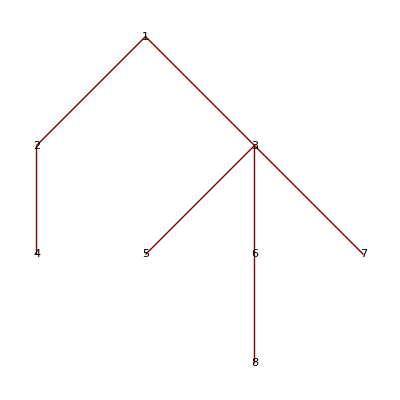
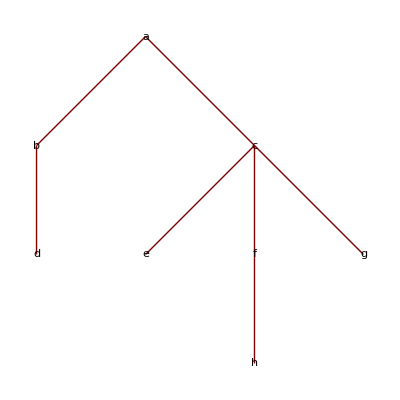

```mathematica
rules1={1->2,1->3,2->4,3->5,3->6,3->7,6->8};
rules2={a->b,a->c,b->d,c->e,c->f,c->g,f->h};
{TreePlot[rules1,VertexLabeling->True],TreePlot[rules2,VertexLabeling->True]}
```

1. Assume that the trees are given as nested lists

```mathematica
tree1={1,{2,{4}},{3,{5},{6,{8}},{7}}};
tree2={a,{b,{d}},{c,{e},{f,{h}},{g}}};
```

```mathematica
Clear[SameStructure];
SameStructure[tree1_?AtomQ,tree2_?AtomQ]:=True;
SameStructure[tree1_List,tree2_List]:=
If[Length[tree1]==Length[tree2],
And@@MapThread[SameStructure,{tree1,tree2},1],
False
];
```

```mathematica
SameStructure[tree1,tree2]
SameStructure[tree1,tree2⟦2⟧]
```

True

False

2. Assume that the trees are given as lists of rules

```mathematica
rules1={1->2,1->3,2->4,3->5,3->6,3->7,6->8};
rules2={a->b,a->c,b->d,c->e,c->f,c->g,f->h};
```

```mathematica
1/.Map[List,rules1]
```

{2,3,1,1,1,1,1}

#### Integer partition

```mathematica
Clear[IntPartitions]
IntPartitions[1]:={{1}};
IntPartitions[2]:={{1,1},{2}};
IntPartitions[n_]:=IntPartitions[n]=Prepend[Union@@Table[Flatten[Outer[Sort[Join[##]]&,IntPartitions[i],IntPartitions[n-i],1],1],{i,1,n/2}],{n}]
```

```mathematica
Clear[IntPartitions]
IntPartitions[1]:={{1}};
IntPartitions[2]:={{1,1},{2}};
IntPartitions[n_]:=IntPartitions[n]=
Block[{t,ip=IntPartitions[n-1]},
Union@Join[Sort[ReplacePart[#,1->#⟦1⟧+1]]&/@ip,Prepend[#,1]&/@ip]
];
```

```mathematica
Clear[IntPartitions]
(*AddOneToEach[partition:{_?NumberQ...}]:=Sort/@Table[ReplacePart[partition,i->partition⟦i⟧+1],{i,1,Length[partition]}];*)
AddOneToEach[p:{_?NumberQ...}]:=
Sort/@(Table[p,{Length[p]}]+IdentityMatrix[Length[p]]);
IntPartitions[1]:={{1}};
IntPartitions[2]:={{1,1},{2}};
IntPartitions[n_]:=IntPartitions[n]=
Block[{t,ip=IntPartitions[n-1]},
Union@Join[Flatten[AddOneToEach/@ip,1],Prepend[#,1]&/@ip]
];
```

```mathematica
IntPartitions[6]
```

{{6},{1,5},{2,4},{3,3},{1,1,4},{1,2,3},{2,2,2},{1,1,1,3},{1,1,2,2},{1,1,1,1,2},{1,1,1,1,1,1}}

```mathematica
IntPartitions[12]//Length
IntegerPartitions[12]//Length
```

77

77

```mathematica
Clear[FerrersDiagram];
Options[FerrersDiagram]={ImageSize->Automatic,Factor->20};
FerrersDiagram[ints_List,psize_?NumberQ,color_,opts:OptionsPattern[]]:=
FerrersDiagram[ints,psize,{color,Black},opts];
FerrersDiagram[ints_List,psize_?NumberQ,{color_,edgeColor_},opts:OptionsPattern[]]:=
Block[{isize=OptionValue[ImageSize],factor=OptionValue[Factor]},
If[isize===Automatic,isize=2psize factor Length[ints]];
Graphics[{color,EdgeForm[edgeColor],Disk[#,psize]&/@Flatten[MapThread[Thread[{#2,#1}]&,{Range/@ints,Range[Length[ints]]},1],1]},ImageSize->isize]
];
```

```mathematica
FerrersDiagram[{4,2,1,1,3},0.4,{Lighter[Orange],Black}]
```

-Graphics-

```mathematica
FerrersDiagram[{3,2,1,1},0.4,{Yellow,Red}]/.Disk[{4,1},r___]:>{Green,Disk[{4,1},r],Blue}
```

-Graphics-

```mathematica
gr1=FerrersDiagram[{1,1,2,2,4},0.4,{Green,Blue}];
gr2=FerrersDiagram[{1,1,2,3,4},0.4,{Green,Blue}];
{gr1,gr2/.Disk[{4,3},r___]:>{Red,Disk[{4,3},r],Blue}}
```

{-Graphics-,-Graphics-}

```mathematica
gr1=FerrersDiagram[{1,2,3,4},0.4,{Green,Blue}];
gr2=FerrersDiagram[{1,1,2,3,4},0.4,{Green,Blue}];
{gr1,gr2/.Disk[{1,1},r___]:>{Red,Disk[{1,1},r],Blue}}
```

{-Graphics-,-Graphics-}

```mathematica
TableForm[Transpose[{#,FerrersDiagram[#,0.42,{GrayLevel[0.8],Black},Factor->16]}&/@IntegerPartitions[6]],TableDepth->2,TableSpacing->{2,3}]
```

{6} | {5,1} | {4,2} | {4,1,1} | {3,3} | {3,2,1} | {3,1,1,1} | {2,2,2} | {2,2,1,1} | {2,1,1,1,1} | {1,1,1,1,1,1}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Transpose[{#,FerrersDiagram[#,0.42,{GrayLevel[0.8],Black},Factor->16]}&/@IntegerPartitions[5]],TableDepth->2,TableSpacing->{2,3}]
```

{5} | {4,1} | {3,2} | {3,1,1} | {2,2,1} | {2,1,1,1} | {1,1,1,1,1}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Proof (WRONG algorithm)

Here we are going to prove that the following recursive procedure would generate for a given number n all the integer partitions IP(n) in reverse lexicographic order. The base case of the recursive procedure is IP(1)={{1}}. In order to derive the integer partitions in IP(n) we append 1 to the all the integer partitions IP(n-1) of n-1 and we add one to the smallest  integer in each partition. If the smallest integer value in the partition is repeated we choose the rightmost one.

Let us proof that with the procedure we just described, we will generate all the partitions for a given integer n. We are going to prove this by induction. Obviously, the partitions of 1 is the set {{1}}, and from this set we derive the partitions for 2 as the set {{1,1},{2}}. So, let us assume that we have the set of integer partitions IP(n-1). In order to derive the integer partitions in IP(n) we append 1 to the all the integer partitions IP(n-1) and we add one to the rightmost smallest  integer value in each partition.

### References

find Roberts (1986) "Thinking recursively"

## String functions and patterns

```mathematica
listFuncs={First, Rest,Length,Part,Take,Append,Join,Reverse,Cases,Position,Count,Select,Drop,Delete,Cases,Partition};
```

```mathematica
stringFuncs=("String"<>ToString[#])&/@listFuncs
```

{StringFirst,StringRest,StringLength,StringPart,StringTake,StringAppend,StringJoin,StringReverse,StringCases,StringPosition,StringCount,StringSelect,StringDrop,StringDelete,StringCases,StringPartition}

```mathematica
standardStringFuncs=Names["String*"]
```

{String,StringBreak,StringByteCount,StringCases,StringCount,StringDrop,StringExpression,StringForm,StringFormat,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPosition,StringQ,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringSkeleton,StringSplit,StringTake,StringToStream,StringTrim}

```mathematica
Intersection[stringFuncs,standardStringFuncs]
```

{StringCases,StringCount,StringDrop,StringJoin,StringLength,StringPosition,StringReverse,StringTake}

## Flow charts

### Table

Simple Table example and flow chart

Two indices Table example and flow chart for them

### Map

### Fold and FoldList

### Cases and Position

## Backus-Naur form

mapStatement = Map[funcName,data]|Map[Function[body],data]

### Matrix multiplication

```mathematica
A=Table[i+j,{i,4},{j,5}];
B=Table[i+j,{i,5},{j,6}];
```

```mathematica
A.B//MatrixForm
```

(90 | 110 | 130 | 150 | 170 | 190
110 | 135 | 160 | 185 | 210 | 235
130 | 160 | 190 | 220 | 250 | 280
150 | 185 | 220 | 255 | 290 | 325)

```mathematica
Outer[Total[MapThread[#1*#2&,{#1,#2}]]&,A,Transpose[B],1]//MatrixForm
```

(90 | 110 | 130 | 150 | 170 | 190
110 | 135 | 160 | 185 | 210 | 235
130 | 160 | 190 | 220 | 250 | 280
150 | 185 | 220 | 255 | 290 | 325)

```mathematica
Outer[Inner[Times,#1,#2,Plus]&,A,Transpose[B],1]//MatrixForm
```

(90 | 110 | 130 | 150 | 170 | 190
110 | 135 | 160 | 185 | 210 | 235
130 | 160 | 190 | 220 | 250 | 280
150 | 185 | 220 | 255 | 290 | 325)

```mathematica
Outer[Inner[Times,#1,#2,Plus]&,#1,Transpose[#2],1]&[A,B]//MatrixForm
```

(90 | 110 | 130 | 150 | 170 | 190
110 | 135 | 160 | 185 | 210 | 235
130 | 160 | 190 | 220 | 250 | 280
150 | 185 | 220 | 255 | 290 | 325)

### Outer implementation

#### Script-like

```mathematica
CartesianProduct[F_, dataArgs___] :=
 Block[{data = {dataArgs}, n, X, x},
  n = Length[data];
  If[n == 1, Map[F, First[data]],
   X = Array[x, n];
   Table[F @@ X, Evaluate[Sequence @@ MapThread[{#1, #2} &, {X, data}]]]
   ]
  ];
```

```mathematica
t = CartesianProduct[F, Range[5], {a, b, c, d}, Range[3]] // MatrixForm
```

((F[1,a,1]
F[1,a,2]
F[1,a,3]) | (F[1,b,1]
F[1,b,2]
F[1,b,3]) | (F[1,c,1]
F[1,c,2]
F[1,c,3]) | (F[1,d,1]
F[1,d,2]
F[1,d,3])
(F[2,a,1]
F[2,a,2]
F[2,a,3]) | (F[2,b,1]
F[2,b,2]
F[2,b,3]) | (F[2,c,1]
F[2,c,2]
F[2,c,3]) | (F[2,d,1]
F[2,d,2]
F[2,d,3])
(F[3,a,1]
F[3,a,2]
F[3,a,3]) | (F[3,b,1]
F[3,b,2]
F[3,b,3]) | (F[3,c,1]
F[3,c,2]
F[3,c,3]) | (F[3,d,1]
F[3,d,2]
F[3,d,3])
(F[4,a,1]
F[4,a,2]
F[4,a,3]) | (F[4,b,1]
F[4,b,2]
F[4,b,3]) | (F[4,c,1]
F[4,c,2]
F[4,c,3]) | (F[4,d,1]
F[4,d,2]
F[4,d,3])
(F[5,a,1]
F[5,a,2]
F[5,a,3]) | (F[5,b,1]
F[5,b,2]
F[5,b,3]) | (F[5,c,1]
F[5,c,2]
F[5,c,3]) | (F[5,d,1]
F[5,d,2]
F[5,d,3]))

#### Non-recursive

```mathematica
Clear[ThreadLeft,ThreadRight];
ThreadLeft[{a_,b_},l_]:=ThreadLeft[List,a,b,l];
ThreadLeft[F_,a_,b_,l_]:=(Map[F[a,#]&,b,{l}]);
ThreadRight[{a_,b_},l_]:=ThreadRight[List,a,b,l];
ThreadRight[F_,a_,b_,l_]:=(Map[F[#,b]&,a,{l}]);
```

```mathematica
ThreadLeft[List,2,{a,b,c,d},1]
```

{{2,a},{2,b},{2,c},{2,d}}

```mathematica
ThreadRight[{{{a,b},{c,d}},2},1]
ThreadRight[{{{a,b},{c,d}},2},2]
```

{{{a,b},2},{{c,d},2}}

{{{a,2},{b,2}},{{c,2},{d,2}}}

```mathematica
Clear[CartesianProduct]
CartesianProduct[F_,dataArgs___]:=CartesianProduct[F,{dataArgs}];
CartesianProduct[F_,dataArgs_List]:=
Block[{n=Length[dataArgs]},
Map[Apply[F,#]&,
Fold[ThreadRight[ThreadLeft[Append,#1,#2,1]&,#1,#2⟦1⟧,#2⟦2⟧]&,List/@First[dataArgs],Transpose[{Rest[dataArgs],Range[1,n-1]}]]
,{n}]
];
```

```mathematica
t=CartesianProduct[F,Range[5],{a,b,c,d},Range[3]]//MatrixForm
```

((F[1,a,1]
F[1,a,2]
F[1,a,3]) | (F[1,b,1]
F[1,b,2]
F[1,b,3]) | (F[1,c,1]
F[1,c,2]
F[1,c,3]) | (F[1,d,1]
F[1,d,2]
F[1,d,3])
(F[2,a,1]
F[2,a,2]
F[2,a,3]) | (F[2,b,1]
F[2,b,2]
F[2,b,3]) | (F[2,c,1]
F[2,c,2]
F[2,c,3]) | (F[2,d,1]
F[2,d,2]
F[2,d,3])
(F[3,a,1]
F[3,a,2]
F[3,a,3]) | (F[3,b,1]
F[3,b,2]
F[3,b,3]) | (F[3,c,1]
F[3,c,2]
F[3,c,3]) | (F[3,d,1]
F[3,d,2]
F[3,d,3])
(F[4,a,1]
F[4,a,2]
F[4,a,3]) | (F[4,b,1]
F[4,b,2]
F[4,b,3]) | (F[4,c,1]
F[4,c,2]
F[4,c,3]) | (F[4,d,1]
F[4,d,2]
F[4,d,3])
(F[5,a,1]
F[5,a,2]
F[5,a,3]) | (F[5,b,1]
F[5,b,2]
F[5,b,3]) | (F[5,c,1]
F[5,c,2]
F[5,c,3]) | (F[5,d,1]
F[5,d,2]
F[5,d,3]))

```mathematica
t//Dimensions
```

{5,4,3}

```mathematica
t=Outer[F,Range[5],{a,b,c,d},Range[3]]//MatrixForm
```

((F[1,a,1]
F[1,a,2]
F[1,a,3]) | (F[1,b,1]
F[1,b,2]
F[1,b,3]) | (F[1,c,1]
F[1,c,2]
F[1,c,3]) | (F[1,d,1]
F[1,d,2]
F[1,d,3])
(F[2,a,1]
F[2,a,2]
F[2,a,3]) | (F[2,b,1]
F[2,b,2]
F[2,b,3]) | (F[2,c,1]
F[2,c,2]
F[2,c,3]) | (F[2,d,1]
F[2,d,2]
F[2,d,3])
(F[3,a,1]
F[3,a,2]
F[3,a,3]) | (F[3,b,1]
F[3,b,2]
F[3,b,3]) | (F[3,c,1]
F[3,c,2]
F[3,c,3]) | (F[3,d,1]
F[3,d,2]
F[3,d,3])
(F[4,a,1]
F[4,a,2]
F[4,a,3]) | (F[4,b,1]
F[4,b,2]
F[4,b,3]) | (F[4,c,1]
F[4,c,2]
F[4,c,3]) | (F[4,d,1]
F[4,d,2]
F[4,d,3])
(F[5,a,1]
F[5,a,2]
F[5,a,3]) | (F[5,b,1]
F[5,b,2]
F[5,b,3]) | (F[5,c,1]
F[5,c,2]
F[5,c,3]) | (F[5,d,1]
F[5,d,2]
F[5,d,3]))

#### Recursive

```mathematica
Clear[CartesianProduct]
CartesianProduct[F_, dataArgs___]:= CartesianProduct[F, {dataArgs}];
CartesianProduct[F_, dataArgs_List]:=
Module[{R,Loop},
R=ConstantArray[0,Length/@dataArgs];
Loop[inds_List]:=
If[Length[inds]==Length[dataArgs],
R⟦Sequence@@inds⟧=F@@MapIndexed[dataArgs⟦#2⟦1⟧,#1⟧&,inds],
Do[Loop[Append[inds,i]],{i,1,Length[dataArgs⟦Length[inds]+1⟧]}]
];
Loop[{}];
R
];
```

```mathematica
Clear[CartesianProduct]
CartesianProduct[F_, dataArgs___]:= CartesianProduct[F, {dataArgs}];
CartesianProduct[F_, dataArgs_List]:=
Module[{R,Loop},
R=ConstantArray[0,Length/@dataArgs];
Loop[inds_List]:=
If[Length[inds]==Length[dataArgs],
R⟦Sequence@@inds⟧=F@@Map[dataArgs⟦Sequence@@#1⟧&,Transpose[{Range[Length[inds]],inds}]],
Do[Loop[Append[inds,i]],{i,1,Length[dataArgs⟦Length[inds]+1⟧]}]
];
Loop[{}];
R
];
```

```mathematica
t = CartesianProduct[F, Range[5], {a, b, c, d},Range[3]] // MatrixForm
```

((F[1,a,1]
F[1,a,2]
F[1,a,3]) | (F[1,b,1]
F[1,b,2]
F[1,b,3]) | (F[1,c,1]
F[1,c,2]
F[1,c,3]) | (F[1,d,1]
F[1,d,2]
F[1,d,3])
(F[2,a,1]
F[2,a,2]
F[2,a,3]) | (F[2,b,1]
F[2,b,2]
F[2,b,3]) | (F[2,c,1]
F[2,c,2]
F[2,c,3]) | (F[2,d,1]
F[2,d,2]
F[2,d,3])
(F[3,a,1]
F[3,a,2]
F[3,a,3]) | (F[3,b,1]
F[3,b,2]
F[3,b,3]) | (F[3,c,1]
F[3,c,2]
F[3,c,3]) | (F[3,d,1]
F[3,d,2]
F[3,d,3])
(F[4,a,1]
F[4,a,2]
F[4,a,3]) | (F[4,b,1]
F[4,b,2]
F[4,b,3]) | (F[4,c,1]
F[4,c,2]
F[4,c,3]) | (F[4,d,1]
F[4,d,2]
F[4,d,3])
(F[5,a,1]
F[5,a,2]
F[5,a,3]) | (F[5,b,1]
F[5,b,2]
F[5,b,3]) | (F[5,c,1]
F[5,c,2]
F[5,c,3]) | (F[5,d,1]
F[5,d,2]
F[5,d,3]))

```mathematica
Outer[F, Range[5], {a, b, c, d},Range[3]] // MatrixForm
```

((F[1,a,1]
F[1,a,2]
F[1,a,3]) | (F[1,b,1]
F[1,b,2]
F[1,b,3]) | (F[1,c,1]
F[1,c,2]
F[1,c,3]) | (F[1,d,1]
F[1,d,2]
F[1,d,3])
(F[2,a,1]
F[2,a,2]
F[2,a,3]) | (F[2,b,1]
F[2,b,2]
F[2,b,3]) | (F[2,c,1]
F[2,c,2]
F[2,c,3]) | (F[2,d,1]
F[2,d,2]
F[2,d,3])
(F[3,a,1]
F[3,a,2]
F[3,a,3]) | (F[3,b,1]
F[3,b,2]
F[3,b,3]) | (F[3,c,1]
F[3,c,2]
F[3,c,3]) | (F[3,d,1]
F[3,d,2]
F[3,d,3])
(F[4,a,1]
F[4,a,2]
F[4,a,3]) | (F[4,b,1]
F[4,b,2]
F[4,b,3]) | (F[4,c,1]
F[4,c,2]
F[4,c,3]) | (F[4,d,1]
F[4,d,2]
F[4,d,3])
(F[5,a,1]
F[5,a,2]
F[5,a,3]) | (F[5,b,1]
F[5,b,2]
F[5,b,3]) | (F[5,c,1]
F[5,c,2]
F[5,c,3]) | (F[5,d,1]
F[5,d,2]
F[5,d,3]))

## Relation with other paradigms

## Exercises

1. Analogy with FORTRAN.

### Patterns

1. Match consecutive numbers within a number sequence. For example, from the sequence:

```mathematica
data={3,2,3,3,3,2,1,2,3,3};
```

we should get the pairs {{2,3},{1,2},{2,3}}.

### Rules

1. Give an alternative pattern for the rule

```mathematica
ReplaceAll[{2,3,Subscript[T, 3],Subscript[A, 4],Subscript[M, 2]},n_Integer->n^2]
```

{4,9,T_9,A_16,M_4}

```mathematica
ReplaceAll[{2,3,Subscript[T, 3],Subscript[A, 4],{Subscript[M, 2],3},{4,{5,Subscript[M, 5]}}},Subscript[s_,n_Integer]:>Subscript[s,n^2]]
```

{2,3,T_9,A_16,{M_4,3},{4,{5,M_25}}}

### Recursion

1. Find a formula for the sum of the first n natural numbers using RSolve.

1.1. Use the recursive definition

s(n)={not defined | n∉ℕ
0 | n≤0
s(n-1)+n | n∈ℕ⋀n>0.

1.2. Solve the functional equation using RSolve:

```mathematica
RSolve[{s[n]==s[n-1]+n,s[0]==0},s[n],n]
```

{{s[n]→1/2 n (1+n)}}

1.3. Define a function named FirstNSum from the result

```mathematica
FirstNSum[n_]:=Evaluate[s[n]/.%⟦1,1⟧]
```

1.4. Apply the function FirstNSum to the range of natural numbers, say from 1 to 20.

```mathematica
FirstNSum[#]&/@Range[1,20]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210}

1.5. Provide alternative code that generates the list above that uses FoldList and it does not use any user defined function.

```mathematica
Rest@FoldList[#1+#2&,0,Range[1,20]]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210}

2. Define a function that reverses elements of list at all levels. For example, the list

```mathematica
{1,2,{21,22,23},{31,{321,322}}}
```

should be reversed as

```mathematica
{{{322,321},31},{23,22,21},2,1}
```

## References

1. Paul Graham, On Lisp,

2. Naur, "Can Programming Be Liberated from the von Neumann Style? A Functional Style and Its Algebra of Programs", 1977 ACM Turing Award Lecture.